silicon, cramped or free  @ both ends
L vs Q^-1 (b=100nm)

300K

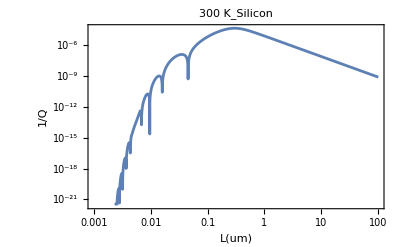

```mathematica
QL300=Abs[3/(4 ξ^3)-ΔE/(Cos[2 d ξ]+Cosh[2 d ξ])(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)]))]/.
{ξ->an/(4 3^(1/4))b^(3/2)/(L √lT)}/.
{d->1.3,lT->1.257 10^-2,an->4.73,ΔE->7.942 10^-5,b->100*10^-3};

QL300g=LogLogPlot[QL300,{L,0.001,100},PlotLabel->300K_Silicon, Frame->True,FrameLabel->{L[um],Q^-1}]
```

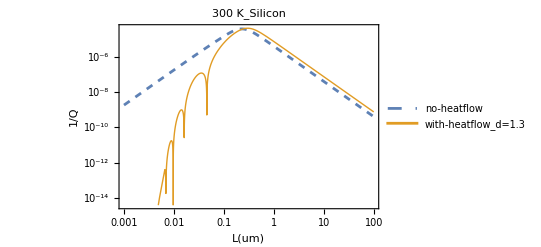

```mathematica
QNoL300 =Abs[ ΔE(6/(2ξ)^2-6/(2ξ)^3(Sinh[2ξ]+Sin[2ξ])/(Cosh[2ξ]+Cos[2ξ]) )]/.
{ξ->an/(4 3^(1/4))b^(3/2)/(L √lT)}/.
{d->1.3,lT->1.257 10^-2,an->4.73,ΔE->7.942 10^-5,b->100*10^-3};
QL300g=LogLogPlot[{QNoL300,QL300},{L,0.001,100},PlotLabel->300K_Silicon, PlotStyle->{Dashed,Thick},PlotLegends->Placed[{"no-heatflow","with-heatflow_d=1.3"},{0.7,0.25}],Frame->True,FrameLabel->{L[um],Q^-1}]
```

100K

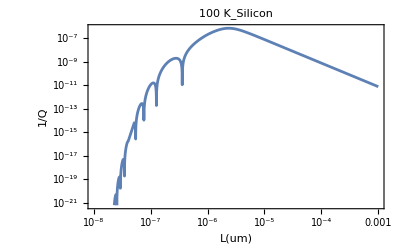

```mathematica
QL100=Abs[3/(4 ξ^3)-ΔE/(Cos[2 d ξ]+Cosh[2 d ξ])(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)]))]/.
{ξ->an/(4 3^(1/4))b^(3/2)/(L √lT)}/.
{d->1.3,lT->2.017 10^-1,an->4.73,ΔE->1.232 10^-6,b->100*100^-3};

QL100g=LogLogPlot[QL100,{L,0.00000001,0.001},PlotLabel->100K_Silicon, Frame->True,FrameLabel->{L[um],Q^-1}]
```

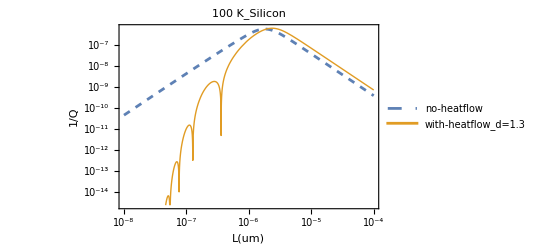

```mathematica
QNoL100 =Abs[ ΔE(6/(2ξ)^2-6/(2ξ)^3(Sinh[2ξ]+Sin[2ξ])/(Cosh[2ξ]+Cos[2ξ]) )]/.
{ξ->an/(4 3^(1/4))b^(3/2)/(L √lT)}/.
{d->1.3,lT->2.017 10^-1,an->4.73,ΔE->1.232 10^-6,b->100*100^-3};
QL100g=LogLogPlot[{QNoL100,QL100},{L,0.00000001,0.0001},PlotLabel->100K_Silicon, PlotStyle->{Dashed,Thick},PlotLegends->Placed[{"no-heatflow","with-heatflow_d=1.3"},{0.7,0.25}],Frame->True,FrameLabel->{L[um],Q^-1}]
```

10K

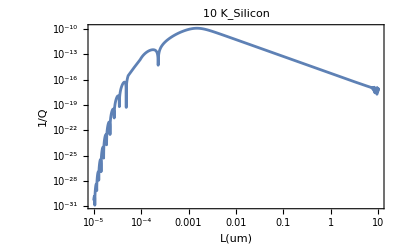

```mathematica
QL10=Abs[3/(4 ξ^3)-ΔE/(Cos[2 d ξ]+Cosh[2 d ξ])(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)]))]/.
{ξ->an/(4 3^(1/4))b^(3/2)/(L √lT)}/.
{d->1.3,lT->4.977 10^2,an->4.73,ΔE->2.319 10^-10,b->100*10^-3};
QL10g=LogLogPlot[QL10,{L,0.00001,10},PlotLabel->10K_Silicon, Frame->True,FrameLabel->{L[um],Q^-1}]
```

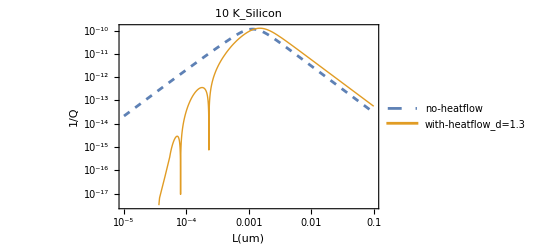

```mathematica
QNoL10 =Abs[ ΔE(6/(2ξ)^2-6/(2ξ)^3(Sinh[2ξ]+Sin[2ξ])/(Cosh[2ξ]+Cos[2ξ]) )]/.
{ξ->an/(4 3^(1/4))b^(3/2)/(L √lT)}/.
{d->1.3,lT->4.977 10^2,an->4.73,ΔE->2.319 10^-10,b->100*10^-3};
QL10g=LogLogPlot[{QNoL10,QL10},{L,0.00001,0.1},PlotLabel->10K_Silicon, PlotStyle->{Dashed,Thick},PlotLegends->Placed[{"no-heatflow","with-heatflow_d=1.3"},{0.7,0.25}],Frame->True,FrameLabel->{L[um],Q^-1}]
```

General::munfl: 1.00099×10^-21 4.76119250443118×10^-2860671は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::munfl: 2.68535×10^-21 4.34765876061154×10^-2058784は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::munfl: 7.20397×10^-21 1.56719240798784×10^-1481677は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::stop: この計算中に，General::munflのこれ以上の出力は表示されません．

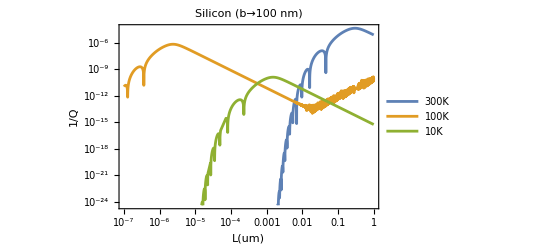

```mathematica
LogLogPlot[{QL300,QL100,QL10},{L,0.0000001,1},PlotLabel-> Silicon ( b->100nm), Frame->True,PlotLegends->Placed[{"300K","100K","10K"},{0.3,0.2}],FrameLabel->{L[um],Q^-1}]
```

General::munfl: 1.00071×10^-21 3.48023353018783×10^-2860940は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::munfl: 2.02502×10^-21 9.22254712758929×10^-2261872は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::munfl: 4.09781×10^-21 1.1191683875185×10^-1788245は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::stop: この計算中に，General::munflのこれ以上の出力は表示されません．

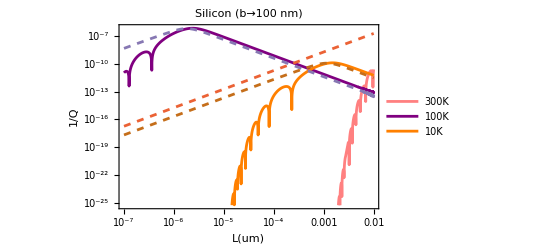

```mathematica
LogLogPlot[{QL300,QL100,QL10,QNoL300,QNoL100,QNoL10},{L,0.0000001,0.01},PlotLabel-> Silicon ( b->100nm),PlotStyle->{Pink,Purple,Orange,Dashed,Dashed,Dashed}, Frame->True,PlotLegends->Placed[{"300K","100K","10K"},{0.3,0.2}],FrameLabel->{L[um],Q^-1}]
```

General::munfl: 1.00071×10^-21 3.48023353018783×10^-2860940は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

Power::infy: 無限式1/0.が見付かりました．

General::munfl: 2.02502×10^-21 9.22254712758929×10^-2261872は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

Power::infy: 無限式1/0.が見付かりました．

General::munfl: 4.09781×10^-21 1.1191683875185×10^-1788245は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::stop: この計算中に，General::munflのこれ以上の出力は表示されません．

Power::infy: 無限式1/0.が見付かりました．

General::stop: この計算中に，Power::infyのこれ以上の出力は表示されません．

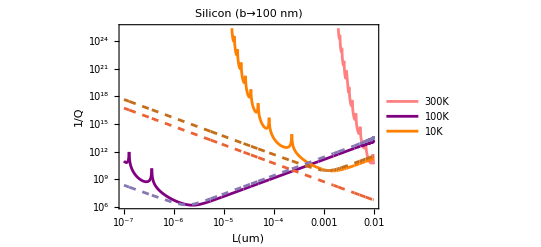

```mathematica
LogLogPlot[{1/QL300,1/QL100,1/QL10,1/QNoL300,1/QNoL100,1/QNoL10},{L,0.0000001,0.01},PlotLabel-> Silicon ( b->100nm),PlotStyle->{Pink,Purple,Orange,Dashed,Dashed,Dashed}, Frame->True,PlotLegends->Placed[{"300K","100K","10K"},{0.3,0.2}],FrameLabel->{L[um],Q^-1}]
```